# Stark effect with Zeeman effect

This software calculates the Stark shift of Rydberg levels in presence of a bias magnetic field, which creates also a Zeeman shift.
The magnetic field is in general not aligned with the electric field, which creates different quantization directions. So one has to include also all the mJ inside (in the case without B, as the Stark interaction term couples levels with the same mL, and thus the same mJ, we could select just the levels with ΔmJ = 0).

The electric field points at the quantization direction of the atoms, the z direction; the magnetic field makes an angle α with the electric field, in the zx plane.

```mathematica
Clear[]
Off[General::"spell1"]
<<"Units`"
<<"PhysicalConstants`"
$MaxPrecision=150;$MachinePrecision;$MaxExtraPrecision=150;$MaxMachineNumber;
```

### Rb^87 data and other constants

Natural constants

```mathematica
hbar=1.054571596*10^-34; (*Js, ref. Steck*)
Head[hbar];
SetPrecision[hbar,15]; (*to show hbar with 15 numbers*)
Precision[hbar] (*hbar is given in Machine Precision*);
h=hbar*2.*π;
Subscript[μ, 0]=4.*π*10^-7 ; (*N/A^2, exact, ref. Steck*)
c=2.99792458*10^8; (*m/s, exact, ref. Steck*)
Subscript[ϵ, 0]=(Subscript[μ, 0] c^2)^-1; (*F/m, exact, ref. Steck*)
Subscript[k, B]=1.3806503*10^-23 ;(*J/K, ref. Steck*)
Subscript[m, e]=9.10938188*10^-31 (*ElectronMass [kg], ref. Steck*);
Subscript[e, SI]=1.602176462*10^-19 (*ElectronCharge [C], ref. Steck*);
Subscript[e, cgs]=Subscript[e, SI]/(4.π Subscript[ϵ, 0])^(1/2);
Subscript[a, 0]=0.5291772083*10^-10; (*m , Bohr Radius, ref. Steck*)
hbar^2/(Subscript[m, e]*Subscript[e, cgs]^2) (*Subscript[a, 0] calculated*);
Subscript[e, cgs]^2/Subscript[a, 0]/Subscript[e, SI] (*atomic energy unit given in [eV=Subscript[e, SI] V]*)
Subscript[μ, B]=9.27400899*10^-24 ;(*J/T , Bohr Magneton, ref. Steck*)
u=1.66053873*10^-27 ;(*kg, Atomic mass unit , ref. Steck*)
α=Subscript[e, SI]^2/(hbar c 4. π Subscript[ϵ, 0]);
SetPrecision[α,9];
Subscript[R, ∞]=(α^2 Subscript[m, e] c)/(4.π hbar) ;(* Rydberg constant: Wikipedia Subscript[R, ∞]=1.0973731568525(73)*10^7 m^-1, slightly different from value calculated with constants from ref. Steck *) 

SetPrecision[Subscript[R, ∞],13] (*to show Subscript[R, ∞] with 13 numbers*)

(*Rubidium*)

Subscript[m, Rb87]=86.909180520*u; (*kg, Atomic Mass^87 Rb, ref. Steck*)
Subscript[R, Rb87]=Subscript[R, ∞]*(1+Subscript[m, e]/Subscript[m, Rb87])^-1 ;(* Subscript[R, Rb]=109736.605 cm^-1 from PRA 67 052502 (2003) Gallagher, "where R_Rb is the Rydberg constant for the reduced electron mass in Rb" -> obviously for Rb85 !! *)
SetPrecision[Subscript[R, Rb87],9] (*to show Subscript[R, ∞] with 9 numbers*)

Subscript[m, Rb85]=84.909180520*u; (*kg, Atomic Mass^85 Rb*)
Subscript[R, Rb85]=Subscript[R, ∞]*(1+Subscript[m, e]/Subscript[m, Rb85])^-1 ;
1-(1+Subscript[m, e]/Subscript[m, Rb85])^-1 (*relative effect of reduced mass (replacing Subscript[R, ∞] by Subscript[R, Rb87]) on Energy is in the order of 6E-6*)
Null

Sqrt[2*Subscript[k, B]/Subscript[m, Rb87]]/2/Pi/86.3*10^3
```

27.2114

1.09737315688×10^7

1.09736623×10^7

6.46074×10^-6

25.5099

### Define Functions for calculation of energy-levels without interaction

Quantum defects taken from Publica
tion T. Gallagher et al. PRA 67, 052502 (2003), n>20. nf_j and ng_j states are found in Han, Gallagher et al. PRA 74 054502 (2006)

```mathematica
Subscript[δ, 0]={3.1311804,2.6548849,2.6416737,1.34809171,1.34646572,0.0165192,0.0165437,0}
Subscript[δ, 2]={0.1784,0.2900,0.2950,-0.60286,-0.59600,-0.085,-0.086,0};


(*list of quantum defects for Rb85 et Rb87 from PRA 67, 052502 (2003) 1^st entry Subscript[ns, 1/2]: lj=1, 2^nd entry Subscript[np, 1/2]:lj=2,3^nd entry Subscript[np, 3/2]:lj=3, 4^th entry Subscript[nd, 3/2]: lj=4, 5^th entry Subscript[nd, 5/2]:lj=5, 6^th entry Subscript[nf, 5/2]:lj=6, 7^th entry Subscript[nf, 7/2]:lj=7,n>20, 8^th entry for levels with l>f quantum defect is set to zero*)

δ[lj_,n_]:=Subscript[δ, 0][[lj]]+(Subscript[δ, 2][[lj]])/(n-Subscript[δ, 0][[lj]])^2; (*Quantum defect for given lj and n for n>20, see T. Gallagher "Rydberg Atoms"*)
δ[7,41]

(*Energy of Rydberg levels with quantum defect (fine structure)*)

En[lj_,n_]:=-(Subscript[R, Rb87] c)/(n-δ[lj,n])^2 (*[Hz], Energy of Level |n,l,j> with quantum effect and mass correction *)
ERadinte[lj_,n_]:=-(0.5*(1+Subscript[m, e]/Subscript[m, Rb87])^-1)/(n-δ[lj,n])^2 (*[Unit=Atomic Energy Unit = Subscript[e, cgs]^2/Subscript[a, 0] [J] = 2 h Subscript[R, ∞] c [J] = 2*Subscript[E, Hydrogen n=1]], "Energy" as needed by "radinte.exe" of Level |n,l,j> with quantum defect and with reduced mass effect, n>20 *)
(*Effect of mass on Energylevels for Rb^87 and Rb^85*)

Enw85[lj_,n_]:=-(Subscript[R, Rb85] c)/n^2 (*[Hz], Energy of Level |n,l,j> without quantum effect for Rb85 *)
SetPrecision[(Enw85[1,51]-Enw85[1,50])*10^-9,15] (*Transition Frequency in GHz for Rb85 to control*);
Enw87[lj_,n_]:=-(Subscript[R, Rb87] c)/n^2 (*[Hz], Energy of Level |n,l,j> without quantum effect for Rb87 *);
SetPrecision[(Enw87[1,51]-Enw87[1,50])*10^-9,15] (*Transition Frequency in GHz for Rb87 to control*);
SetPrecision[(Enw87[1,51]-Enw87[1,50])-(Enw85[1,51]-Enw85[1,50]),15] (* Difference for Transition Frequencies in Hz for Rb87 and Rb85, effect in the order of 10kHz *)

(*Define Function Choose to choose lj for quantum defect as a function of l and j*)
Chooselj[l_,j_]:=If[j==1/2,lj=1]/;l==0  (*s states*)
Chooselj[l_,j_]:=If[j==1/2,lj=2,lj=3]/;l==1 (*p states*)
Chooselj[l_,j_]:=If[j==3/2,lj=4,lj=5]/;l==2 (*d states*)
Chooselj[l_,j_]:=If[j==5/2,lj=6,lj=7]/;l==3 (*f states*)
Chooselj[l_,j_]:=If[j==7/2,lj=8,lj=8]/;l>3 (*higher than f states*)
```

{3.13118,2.65488,2.64167,1.34809,1.34647,0.0165192,0.0165437,0}

0.0164925

7597.31420898438

### Integration of C-Code for Numerov Integration to calculate radial matrix elements, Tests of accuracy by comparison to Hydrogen

Install the external program "radinte.exe" which will be used to calculate the radial matrix element <E1,l1!R**I!E2,l2> by Numerov Integration in atomic length unit [a_0^I]   with the following Mathematica syntax: "RadIntE[E1_Real,E2_Real,l1_Integer,l2_Integer,I_Integer]".  l1 and l2 are magnetic quantum numbers. E1 and E2 are the Energies of the levels |n,l,j> calculated with quantum defect and with mass correction in atomic energy units ([e_cgs)^2/a_0] done by ERadinte[lj_,n_].
Attention: The Real numbers E1 and E2 have to be in floating point representation, otherwise Mathlink (communication between radinte.exe and Mathematica) will hang up!! The calculation in radinte.exe is done in double precision.

```mathematica
Install["D:\\Doktorarbeit\\Simus\\Mathematica\\radinte\\radinte\\Debug\\radinte.exe"]
?RadIntE

(*Test: Comparison with existing .exe file *)
RadIntE[
  ERadinte[1,50],-0.0453211,0,1,1]
RadIntE[-0.0453211,ERadinte[1,50],1,0,1]
RadIntE[-0.03661927,ERadinte[1,50],1,0,1]
Timing[RadIntE[-0.03661928,-0.0002276161,1,0,1]]
```

LinkObject["D:\Documents\raulcteixeira\Documents\Simulations et calculs\Simulation_Rydberg + taille du BEC dans piège magnétique\Spectres VdW\radinte\radinte.exe",14,12]

RadIntE[E1_Real,E2_Real,l1_Integer,l2_Integer,I_Integer] calculates radial matrix element <E1,l1!R**I!E2,l2> by Numerov Integration.

-0.0267742

-0.0267742

0.00740212

{0.,0.00741686}

## | 61 p1/2 >

#### Definition of coupling between levels due to magnetic field (Zeeman effect)

```mathematica
(*Calculation of Zeeman term <n,l,j,m| μ*B |np,lp,jp,mp> *)


RZeeman [{n_,l_,lj_},{np_,lp_,ljp_}]:=RadIntE[ERadinte[lj,n],ERadinte[ljp,np],l,lp,0];
RZeeman [{60,0,1},{60,0,1}]
RZeeman [{100,0,1},{100,0,1}]
RZeeman [{60,0,1},{59,0,1}]
RZeeman [{60,1,3},{60,1,3}]
RZeeman [{60,1,3},{59,1,3}]

(*Landé g-factor*)
g[l_,j_] := 3/2+(3/4-l*(l+1))/(2*j*(j+1));

g[0,1/2]
g[1,1/2]
BMatrixelement[{n_,l_,j_,m_},{np_,lp_,jp_,mp_},α_]:=RZeeman [{np,lp,Chooselj[lp,jp]},{n,l,Chooselj[l,j]}]  *  g[lp,jp]* KroneckerDelta[lp,l]*KroneckerDelta[jp,j]* (Cos[α]*mp*KroneckerDelta[mp,m]+Sin[α]/2*(Sqrt[jp*(jp+1)-mp*(mp+1)]*KroneckerDelta[mp+1,m]+Sqrt[jp*(jp+1)-mp*(mp-1)]*KroneckerDelta[mp-1,m])  );

BMatrixelement[{60,0,1/2,1/2},{60,0,1/2,1/2},0]*Subscript[μ, B]/h/10^9*10^(-4) (*Zeeman effect, GHz per Gauss, for s fine levels *)
BMatrixelement[{60,1,3/2,3/2},{60,1,3/2,3/2},0]*Subscript[μ, B]/h/10^9*10^(-4)  (*Zeeman effect, GHz per Gauss, for p 3/2 fine levels *)
```

1.

1.

-0.000405891

1.

-0.00041805

2

2/3

0.00139962

0.00279925

#### Definition of coupling between levels due to electric field (Stark effect)

```mathematica
(*Calculation of r-Vector-Matrixelement <n,l,j,m|{x,y,z}|np,lp,jp,mp>(Vector) = RDip*ADip(Vector) for Angular and Radial Part (in atomic unit [Subscript[a, 0]]), ADip is a 3x1 Vector! *)
ADip[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=(√2)/2*(-1.)^(jp+l-1/2)*√(2.*jp+1)*SixJSymbol[{lp,1/2,jp},{j,1,l}]*(-1)^l*√((2*l+1)*(2*lp+1))*ThreeJSymbol[{l,0},{1,0},{lp,0}]*{ClebschGordan[{jp,mp},{1,-1},{j,m}]-ClebschGordan[{jp,mp},{1,1},{j,m}],I*ClebschGordan[{jp,mp},{1,-1},{j,m}]+I*ClebschGordan[{jp,mp},{1,1},{j,m}],√2*ClebschGordan[{jp,mp},{1,0},{j,m}]};
RDip[{n_,l_,lj_},{np_,lp_,ljp_}]:=RadIntE[ERadinte[lj,n],ERadinte[ljp,np],l,lp,1];

RDip[{1,0,1},{1,0,1}]

(*  Definition of Matrix Element Subscript[H, dipole]= RDip*ADip(Vector)(*.EField*) in unit [Subscript[a, 0]*Subscript[e, SI](*V/m*)]  *)
EMatrixelement[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=RDip[{n,l,Chooselj[l,j]},{np,lp,Chooselj[lp,jp]}]*ADip[{n,l,j,m},{np,lp,jp,mp}](*.EField*);

EMatrixelement[{60,1,3/2,3/2},{60,2,3/2,3/2}]*Subscript[e, SI]*Subscript[a, 0]/h
EMatrixelement[{60,1,3/2,-1/2},{60,2,3/2,-1/2}]*Subscript[e, SI]*Subscript[a, 0]/h
EMatrixelement[{60,1,3/2,-1/2},{61,1,1/2,-1/2}]*Subscript[e, SI]*Subscript[a, 0]/h
```

7.07037

ClebschGordan::phy: ThreeJSymbol[{3/2, 3/2}, {1, -1}, {3/2, -3/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, 3/2}, {1, 1}, {3/2, -3/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, 3/2}, {1, -1}, {3/2, -3/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,94836.5}

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, 1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,-31612.2}

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 1}, {3/2, 1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {3/2, 1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{0.,0.,0.}

#### Selection of Hilbert basis for the calculation, centered at |60p3/2>

```mathematica
(*Define Initial levels*)
(*Atom1, |n_(1,)Subscript[l, 1],Subscript[s, 1],Subscript[j, 1],Subscript[m, 1]>*)
Subscript[n, 1]=60;Subscript[l, 1]=1;Subscript[j, 1]=1/2;Subscript[m, 1]=-1/2;

Bfield =8.5*10^(-4); (* Magnetic field in Tesla *)
αB =0; (* angle between electric field and magnetic field, in radians *)

lj1=Chooselj[Subscript[l, 1],Subscript[j, 1]];
Subscript[E, 12]=En[lj1,Subscript[n, 1]]

(*Set up Basis for Hilbertspace*)
Subscript[n, min]=50; Subscript[n, max]=70;

δf=40*10^9; 

Clear[NList,i,k,n,l,ljA,ljB,EA,EB,EAB,t]
t=0;
NList={};
Timing[For[i=Subscript[n, min],i≤Subscript[n, max],i++, 
	For[Subscript[l, A]=0,Subscript[l, A]≤i-1,Subscript[l, A]++,
	For[ Subscript[j, A]=Abs[Subscript[l, A]-1/2],Subscript[j, A]≤Subscript[l, A]+1/2,Subscript[j, A]++, 
			ljA=Chooselj[Subscript[l, A],Subscript[j, A]];
				EA=En[ljA,i];
				EAB = BMatrixelement[{i,Subscript[l, A],Subscript[j, A],Subscript[m, A]},{i,Subscript[l, A],Subscript[j, A],Subscript[m, A]},αB]*Subscript[μ, B]/h*Bfield;
				If[(Subscript[E, 12]-δf)<EA<(Subscript[E, 12]+δf),For[Subscript[m, A]=-Subscript[j, A],Subscript[m, A]≤Subscript[j, A],Subscript[m, A]++,If[Abs[Subscript[m, A]-Subscript[m, 1]]≤2,t++;NList=Join[NList,{{i,Subscript[l, A],Subscript[j, A],Subscript[m, A],EA+EAB,(-1)^Subscript[l, A]}}]]]]]
]]
]
Length[NList]

Subscript[Ecorr, 12]=En[lj1,Subscript[n, 1]]+BMatrixelement[{Subscript[n, 1],Subscript[l, 1],Subscript[j, 1],Subscript[m, 1]},{Subscript[n, 1],Subscript[l, 1],Subscript[j, 1],Subscript[m, 1]},0]*Subscript[μ, B]/h*Bfield;
Subscript[Ecorr, 12] -Subscript[E, 12]

NList

(* NList is organized by the principal number n *)
NList[[Ordering[NList[[All,{1}]]]]];
```

-1.00042×10^12

{0.561,Null}

1130

-3.9656×10^6

{{57,3,5/2,-5/2,-1.01314×10^12,-1},{57,3,5/2,-3/2,-1.01314×10^12,-1},{57,3,5/2,-1/2,-1.01314×10^12,-1},{57,3,5/2,1/2,-1.01314×10^12,-1},{57,3,5/2,3/2,-1.01314×10^12,-1},{57,3,7/2,-5/2,-1.0131×10^12,-1},{57,3,7/2,-3/2,-1.0131×10^12,-1},«1116»,{61,0,1/2,1/2,-9.8233×10^11,1},{61,1,1/2,-1/2,-9.66405×10^11,-1},{61,1,1/2,1/2,-9.66405×10^11,-1},{61,1,3/2,-3/2,-9.65956×10^11,-1},{61,1,3/2,-1/2,-9.65956×10^11,-1},{61,1,3/2,1/2,-9.65956×10^11,-1},{61,1,3/2,3/2,-9.65956×10^11,-1}}

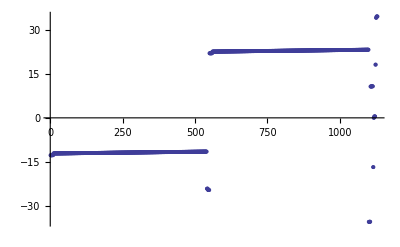

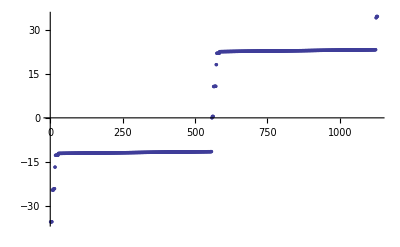

```mathematica
(*Find minimal Energydistance of found levels to initial levels*)

Clear[EDiff]
EDiff={};
For[i=1,i≤Length[NList],i++,EDiff=Join[EDiff,{(NList[[i,5]]-Subscript[E, 12])/10^9}]];
ListPlot[EDiff, PlotRange->{All,All},PlotStyle->PointSize[0.007]]
ListPlot[EDiff[[Ordering[EDiff]]], PlotRange->{All,All},PlotStyle->PointSize[0.006]]
```

#### Creation of a list with the label of each level

```mathematica
NListTemp=NList[[Ordering[NList[[All,{5}]]]]] ;

(*Ordering NList beginning with highest Energy
LabelList is organized by energy also; it's an index for the NListTemp *)

LabelList={};
For[i=1,i≤Length[NList],i++,LabelList=Join[LabelList,{NListTemp[[i,1]]|NListTemp[[i,2]]|NListTemp[[i,3]]|NListTemp[[i,4]]}]]

(*Make List of Hilbert Space Basis level names for Plot of Energies*)

NList ;
LabelList

Clear[n,l,m,j,mj,np,lp,mp,jp,mjp,lj,ljp,Ξ,Ω,Ex,Ey,Ez,EField]
Clear[I0,E0,EFieldpi,EFieldsp,EFieldsm]
```

{59|1|1/2|-1/2,59|1|1/2|1/2,59|1|3/2|-3/2,59|1|3/2|-1/2,59|1|3/2|1/2,59|1|3/2|3/2,58|2|5/2|-5/2,58|2|5/2|-3/2,58|2|5/2|-1/2,58|2|5/2|1/2,58|2|5/2|3/2,58|2|3/2|-3/2,58|2|3/2|-1/2,58|2|3/2|1/2,58|2|3/2|3/2,60|0|1/2|-1/2,60|0|1/2|1/2,57|3|5/2|-5/2,57|3|5/2|-3/2,57|3|5/2|-1/2,57|3|5/2|1/2,57|3|5/2|3/2,57|3|7/2|-5/2,57|3|7/2|-3/2,57|3|7/2|-1/2,57|3|7/2|1/2,57|3|7/2|3/2,57|4|7/2|-5/2,57|4|7/2|-3/2,57|4|7/2|-1/2,57|4|7/2|1/2,57|4|7/2|3/2,57|4|9/2|-5/2,57|4|9/2|-3/2,57|4|9/2|-1/2,57|4|9/2|1/2,57|4|9/2|3/2,57|5|9/2|-5/2,57|5|9/2|-3/2,57|5|9/2|-1/2,57|5|9/2|1/2,57|5|9/2|3/2,57|5|11/2|-5/2,57|5|11/2|-3/2,57|5|11/2|-1/2,57|5|11/2|1/2,57|5|11/2|3/2,57|6|11/2|-5/2,57|6|11/2|-3/2,57|6|11/2|-1/2,57|6|11/2|1/2,57|6|11/2|3/2,57|6|13/2|-5/2,57|6|13/2|-3/2,57|6|13/2|-1/2,57|6|13/2|1/2,57|6|13/2|3/2,57|7|13/2|-5/2,57|7|13/2|-3/2,57|7|13/2|-1/2,57|7|13/2|1/2,57|7|13/2|3/2,57|7|15/2|-5/2,57|7|15/2|-3/2,57|7|15/2|-1/2,57|7|15/2|1/2,57|7|15/2|3/2,57|8|15/2|-5/2,57|8|15/2|-3/2,57|8|15/2|-1/2,57|8|15/2|1/2,57|8|15/2|3/2,57|8|17/2|-5/2,57|8|17/2|-3/2,57|8|17/2|-1/2,57|8|17/2|1/2,57|8|17/2|3/2,57|9|17/2|-5/2,57|9|17/2|-3/2,57|9|17/2|-1/2,57|9|17/2|1/2,57|9|17/2|3/2,57|9|19/2|-5/2,57|9|19/2|-3/2,57|9|19/2|-1/2,57|9|19/2|1/2,57|9|19/2|3/2,57|10|19/2|-5/2,57|10|19/2|-3/2,57|10|19/2|-1/2,57|10|19/2|1/2,57|10|19/2|3/2,57|10|21/2|-5/2,57|10|21/2|-3/2,57|10|21/2|-1/2,57|10|21/2|1/2,57|10|21/2|3/2,57|11|21/2|-5/2,57|11|21/2|-3/2,57|11|21/2|-1/2,57|11|21/2|1/2,57|11|21/2|3/2,57|11|23/2|-5/2,57|11|23/2|-3/2,57|11|23/2|-1/2,57|11|23/2|1/2,57|11|23/2|3/2,57|12|23/2|-5/2,57|12|23/2|-3/2,57|12|23/2|-1/2,57|12|23/2|1/2,57|12|23/2|3/2,57|12|25/2|-5/2,57|12|25/2|-3/2,57|12|25/2|-1/2,57|12|25/2|1/2,57|12|25/2|3/2,57|13|25/2|-5/2,57|13|25/2|-3/2,57|13|25/2|-1/2,57|13|25/2|1/2,57|13|25/2|3/2,57|13|27/2|-5/2,57|13|27/2|-3/2,57|13|27/2|-1/2,57|13|27/2|1/2,57|13|27/2|3/2,57|14|27/2|-5/2,57|14|27/2|-3/2,57|14|27/2|-1/2,57|14|27/2|1/2,57|14|27/2|3/2,57|14|29/2|-5/2,57|14|29/2|-3/2,57|14|29/2|-1/2,57|14|29/2|1/2,57|14|29/2|3/2,57|15|29/2|-5/2,57|15|29/2|-3/2,57|15|29/2|-1/2,57|15|29/2|1/2,57|15|29/2|3/2,57|15|31/2|-5/2,57|15|31/2|-3/2,57|15|31/2|-1/2,57|15|31/2|1/2,57|15|31/2|3/2,57|16|31/2|-5/2,57|16|31/2|-3/2,57|16|31/2|-1/2,57|16|31/2|1/2,57|16|31/2|3/2,57|16|33/2|-5/2,57|16|33/2|-3/2,57|16|33/2|-1/2,57|16|33/2|1/2,57|16|33/2|3/2,57|17|33/2|-5/2,57|17|33/2|-3/2,57|17|33/2|-1/2,57|17|33/2|1/2,57|17|33/2|3/2,57|17|35/2|-5/2,57|17|35/2|-3/2,57|17|35/2|-1/2,57|17|35/2|1/2,57|17|35/2|3/2,57|18|35/2|-5/2,57|18|35/2|-3/2,57|18|35/2|-1/2,57|18|35/2|1/2,57|18|35/2|3/2,57|18|37/2|-5/2,57|18|37/2|-3/2,57|18|37/2|-1/2,57|18|37/2|1/2,57|18|37/2|3/2,57|19|37/2|-5/2,57|19|37/2|-3/2,57|19|37/2|-1/2,57|19|37/2|1/2,57|19|37/2|3/2,57|19|39/2|-5/2,57|19|39/2|-3/2,57|19|39/2|-1/2,57|19|39/2|1/2,57|19|39/2|3/2,57|20|39/2|-5/2,57|20|39/2|-3/2,57|20|39/2|-1/2,57|20|39/2|1/2,57|20|39/2|3/2,57|20|41/2|-5/2,57|20|41/2|-3/2,57|20|41/2|-1/2,57|20|41/2|1/2,57|20|41/2|3/2,57|21|41/2|-5/2,57|21|41/2|-3/2,57|21|41/2|-1/2,57|21|41/2|1/2,57|21|41/2|3/2,57|21|43/2|-5/2,57|21|43/2|-3/2,57|21|43/2|-1/2,57|21|43/2|1/2,57|21|43/2|3/2,57|22|43/2|-5/2,57|22|43/2|-3/2,57|22|43/2|-1/2,57|22|43/2|1/2,57|22|43/2|3/2,57|22|45/2|-5/2,57|22|45/2|-3/2,57|22|45/2|-1/2,57|22|45/2|1/2,57|22|45/2|3/2,57|23|45/2|-5/2,57|23|45/2|-3/2,57|23|45/2|-1/2,57|23|45/2|1/2,57|23|45/2|3/2,57|23|47/2|-5/2,57|23|47/2|-3/2,57|23|47/2|-1/2,57|23|47/2|1/2,57|23|47/2|3/2,57|24|47/2|-5/2,57|24|47/2|-3/2,57|24|47/2|-1/2,57|24|47/2|1/2,57|24|47/2|3/2,57|24|49/2|-5/2,57|24|49/2|-3/2,57|24|49/2|-1/2,57|24|49/2|1/2,57|24|49/2|3/2,57|25|49/2|-5/2,57|25|49/2|-3/2,57|25|49/2|-1/2,57|25|49/2|1/2,57|25|49/2|3/2,57|25|51/2|-5/2,57|25|51/2|-3/2,57|25|51/2|-1/2,57|25|51/2|1/2,57|25|51/2|3/2,57|26|51/2|-5/2,57|26|51/2|-3/2,57|26|51/2|-1/2,57|26|51/2|1/2,57|26|51/2|3/2,57|26|53/2|-5/2,57|26|53/2|-3/2,57|26|53/2|-1/2,57|26|53/2|1/2,57|26|53/2|3/2,57|27|53/2|-5/2,57|27|53/2|-3/2,57|27|53/2|-1/2,57|27|53/2|1/2,57|27|53/2|3/2,57|27|55/2|-5/2,57|27|55/2|-3/2,57|27|55/2|-1/2,57|27|55/2|1/2,57|27|55/2|3/2,57|28|55/2|-5/2,57|28|55/2|-3/2,57|28|55/2|-1/2,57|28|55/2|1/2,57|28|55/2|3/2,57|28|57/2|-5/2,57|28|57/2|-3/2,57|28|57/2|-1/2,57|28|57/2|1/2,57|28|57/2|3/2,57|29|57/2|-5/2,57|29|57/2|-3/2,57|29|57/2|-1/2,57|29|57/2|1/2,57|29|57/2|3/2,57|29|59/2|-5/2,57|29|59/2|-3/2,57|29|59/2|-1/2,57|29|59/2|1/2,57|29|59/2|3/2,57|30|59/2|-5/2,57|30|59/2|-3/2,57|30|59/2|-1/2,57|30|59/2|1/2,57|30|59/2|3/2,57|30|61/2|-5/2,57|30|61/2|-3/2,57|30|61/2|-1/2,57|30|61/2|1/2,57|30|61/2|3/2,57|31|61/2|-5/2,57|31|61/2|-3/2,57|31|61/2|-1/2,57|31|61/2|1/2,57|31|61/2|3/2,57|31|63/2|-5/2,57|31|63/2|-3/2,57|31|63/2|-1/2,57|31|63/2|1/2,57|31|63/2|3/2,57|32|63/2|-5/2,57|32|63/2|-3/2,57|32|63/2|-1/2,57|32|63/2|1/2,57|32|63/2|3/2,57|32|65/2|-5/2,57|32|65/2|-3/2,57|32|65/2|-1/2,57|32|65/2|1/2,57|32|65/2|3/2,57|33|65/2|-5/2,57|33|65/2|-3/2,57|33|65/2|-1/2,57|33|65/2|1/2,57|33|65/2|3/2,57|33|67/2|-5/2,57|33|67/2|-3/2,57|33|67/2|-1/2,57|33|67/2|1/2,57|33|67/2|3/2,57|34|67/2|-5/2,57|34|67/2|-3/2,57|34|67/2|-1/2,57|34|67/2|1/2,57|34|67/2|3/2,57|34|69/2|-5/2,57|34|69/2|-3/2,57|34|69/2|-1/2,57|34|69/2|1/2,57|34|69/2|3/2,57|35|69/2|-5/2,57|35|69/2|-3/2,57|35|69/2|-1/2,57|35|69/2|1/2,57|35|69/2|3/2,57|35|71/2|-5/2,57|35|71/2|-3/2,57|35|71/2|-1/2,57|35|71/2|1/2,57|35|71/2|3/2,57|36|71/2|-5/2,57|36|71/2|-3/2,57|36|71/2|-1/2,57|36|71/2|1/2,57|36|71/2|3/2,57|36|73/2|-5/2,57|36|73/2|-3/2,57|36|73/2|-1/2,57|36|73/2|1/2,57|36|73/2|3/2,57|37|73/2|-5/2,57|37|73/2|-3/2,57|37|73/2|-1/2,57|37|73/2|1/2,57|37|73/2|3/2,57|37|75/2|-5/2,57|37|75/2|-3/2,57|37|75/2|-1/2,57|37|75/2|1/2,57|37|75/2|3/2,57|38|75/2|-5/2,57|38|75/2|-3/2,57|38|75/2|-1/2,57|38|75/2|1/2,57|38|75/2|3/2,57|38|77/2|-5/2,57|38|77/2|-3/2,57|38|77/2|-1/2,57|38|77/2|1/2,57|38|77/2|3/2,57|39|77/2|-5/2,57|39|77/2|-3/2,57|39|77/2|-1/2,57|39|77/2|1/2,57|39|77/2|3/2,57|39|79/2|-5/2,57|39|79/2|-3/2,57|39|79/2|-1/2,57|39|79/2|1/2,57|39|79/2|3/2,57|40|79/2|-5/2,57|40|79/2|-3/2,57|40|79/2|-1/2,57|40|79/2|1/2,57|40|79/2|3/2,57|40|81/2|-5/2,57|40|81/2|-3/2,57|40|81/2|-1/2,57|40|81/2|1/2,57|40|81/2|3/2,57|41|81/2|-5/2,57|41|81/2|-3/2,57|41|81/2|-1/2,57|41|81/2|1/2,57|41|81/2|3/2,57|41|83/2|-5/2,57|41|83/2|-3/2,57|41|83/2|-1/2,57|41|83/2|1/2,57|41|83/2|3/2,57|42|83/2|-5/2,57|42|83/2|-3/2,57|42|83/2|-1/2,57|42|83/2|1/2,57|42|83/2|3/2,57|42|85/2|-5/2,57|42|85/2|-3/2,57|42|85/2|-1/2,57|42|85/2|1/2,57|42|85/2|3/2,57|43|85/2|-5/2,57|43|85/2|-3/2,57|43|85/2|-1/2,57|43|85/2|1/2,57|43|85/2|3/2,57|43|87/2|-5/2,57|43|87/2|-3/2,57|43|87/2|-1/2,57|43|87/2|1/2,57|43|87/2|3/2,57|44|87/2|-5/2,57|44|87/2|-3/2,57|44|87/2|-1/2,57|44|87/2|1/2,57|44|87/2|3/2,57|44|89/2|-5/2,57|44|89/2|-3/2,57|44|89/2|-1/2,57|44|89/2|1/2,57|44|89/2|3/2,57|45|89/2|-5/2,57|45|89/2|-3/2,57|45|89/2|-1/2,57|45|89/2|1/2,57|45|89/2|3/2,57|45|91/2|-5/2,57|45|91/2|-3/2,57|45|91/2|-1/2,57|45|91/2|1/2,57|45|91/2|3/2,57|46|91/2|-5/2,57|46|91/2|-3/2,57|46|91/2|-1/2,57|46|91/2|1/2,57|46|91/2|3/2,57|46|93/2|-5/2,57|46|93/2|-3/2,57|46|93/2|-1/2,57|46|93/2|1/2,57|46|93/2|3/2,57|47|93/2|-5/2,57|47|93/2|-3/2,57|47|93/2|-1/2,57|47|93/2|1/2,57|47|93/2|3/2,57|47|95/2|-5/2,57|47|95/2|-3/2,57|47|95/2|-1/2,57|47|95/2|1/2,57|47|95/2|3/2,57|48|95/2|-5/2,57|48|95/2|-3/2,57|48|95/2|-1/2,57|48|95/2|1/2,57|48|95/2|3/2,57|48|97/2|-5/2,57|48|97/2|-3/2,57|48|97/2|-1/2,57|48|97/2|1/2,57|48|97/2|3/2,57|49|97/2|-5/2,57|49|97/2|-3/2,57|49|97/2|-1/2,57|49|97/2|1/2,57|49|97/2|3/2,57|49|99/2|-5/2,57|49|99/2|-3/2,57|49|99/2|-1/2,57|49|99/2|1/2,57|49|99/2|3/2,57|50|99/2|-5/2,57|50|99/2|-3/2,57|50|99/2|-1/2,57|50|99/2|1/2,57|50|99/2|3/2,57|50|101/2|-5/2,57|50|101/2|-3/2,57|50|101/2|-1/2,57|50|101/2|1/2,57|50|101/2|3/2,57|51|101/2|-5/2,57|51|101/2|-3/2,57|51|101/2|-1/2,57|51|101/2|1/2,57|51|101/2|3/2,57|51|103/2|-5/2,57|51|103/2|-3/2,57|51|103/2|-1/2,57|51|103/2|1/2,57|51|103/2|3/2,57|52|103/2|-5/2,57|52|103/2|-3/2,57|52|103/2|-1/2,57|52|103/2|1/2,57|52|103/2|3/2,57|52|105/2|-5/2,57|52|105/2|-3/2,57|52|105/2|-1/2,57|52|105/2|1/2,57|52|105/2|3/2,57|53|105/2|-5/2,57|53|105/2|-3/2,57|53|105/2|-1/2,57|53|105/2|1/2,57|53|105/2|3/2,57|53|107/2|-5/2,57|53|107/2|-3/2,57|53|107/2|-1/2,57|53|107/2|1/2,57|53|107/2|3/2,57|54|107/2|-5/2,57|54|107/2|-3/2,57|54|107/2|-1/2,57|54|107/2|1/2,57|54|107/2|3/2,57|54|109/2|-5/2,57|54|109/2|-3/2,57|54|109/2|-1/2,57|54|109/2|1/2,57|54|109/2|3/2,57|55|109/2|-5/2,57|55|109/2|-3/2,57|55|109/2|-1/2,57|55|109/2|1/2,57|55|109/2|3/2,57|55|111/2|-5/2,57|55|111/2|-3/2,57|55|111/2|-1/2,57|55|111/2|1/2,57|55|111/2|3/2,57|56|111/2|-5/2,57|56|111/2|-3/2,57|56|111/2|-1/2,57|56|111/2|1/2,57|56|111/2|3/2,57|56|113/2|-5/2,57|56|113/2|-3/2,57|56|113/2|-1/2,57|56|113/2|1/2,57|56|113/2|3/2,60|1|1/2|-1/2,60|1|1/2|1/2,60|1|3/2|-3/2,60|1|3/2|-1/2,60|1|3/2|1/2,60|1|3/2|3/2,59|2|3/2|-3/2,59|2|3/2|-1/2,59|2|3/2|1/2,59|2|3/2|3/2,59|2|5/2|-5/2,59|2|5/2|-3/2,59|2|5/2|-1/2,59|2|5/2|1/2,59|2|5/2|3/2,61|0|1/2|-1/2,61|0|1/2|1/2,58|3|5/2|-5/2,58|3|5/2|-3/2,58|3|5/2|-1/2,58|3|5/2|1/2,58|3|5/2|3/2,58|3|7/2|-5/2,58|3|7/2|-3/2,58|3|7/2|-1/2,58|3|7/2|1/2,58|3|7/2|3/2,58|4|7/2|-5/2,58|4|7/2|-3/2,58|4|7/2|-1/2,58|4|7/2|1/2,58|4|7/2|3/2,58|4|9/2|-5/2,58|4|9/2|-3/2,58|4|9/2|-1/2,58|4|9/2|1/2,58|4|9/2|3/2,58|5|9/2|-5/2,58|5|9/2|-3/2,58|5|9/2|-1/2,58|5|9/2|1/2,58|5|9/2|3/2,58|5|11/2|-5/2,58|5|11/2|-3/2,58|5|11/2|-1/2,58|5|11/2|1/2,58|5|11/2|3/2,58|6|11/2|-5/2,58|6|11/2|-3/2,58|6|11/2|-1/2,58|6|11/2|1/2,58|6|11/2|3/2,58|6|13/2|-5/2,58|6|13/2|-3/2,58|6|13/2|-1/2,58|6|13/2|1/2,58|6|13/2|3/2,58|7|13/2|-5/2,58|7|13/2|-3/2,58|7|13/2|-1/2,58|7|13/2|1/2,58|7|13/2|3/2,58|7|15/2|-5/2,58|7|15/2|-3/2,58|7|15/2|-1/2,58|7|15/2|1/2,58|7|15/2|3/2,58|8|15/2|-5/2,58|8|15/2|-3/2,58|8|15/2|-1/2,58|8|15/2|1/2,58|8|15/2|3/2,58|8|17/2|-5/2,58|8|17/2|-3/2,58|8|17/2|-1/2,58|8|17/2|1/2,58|8|17/2|3/2,58|9|17/2|-5/2,58|9|17/2|-3/2,58|9|17/2|-1/2,58|9|17/2|1/2,58|9|17/2|3/2,58|9|19/2|-5/2,58|9|19/2|-3/2,58|9|19/2|-1/2,58|9|19/2|1/2,58|9|19/2|3/2,58|10|19/2|-5/2,58|10|19/2|-3/2,58|10|19/2|-1/2,58|10|19/2|1/2,58|10|19/2|3/2,58|10|21/2|-5/2,58|10|21/2|-3/2,58|10|21/2|-1/2,58|10|21/2|1/2,58|10|21/2|3/2,58|11|21/2|-5/2,58|11|21/2|-3/2,58|11|21/2|-1/2,58|11|21/2|1/2,58|11|21/2|3/2,58|11|23/2|-5/2,58|11|23/2|-3/2,58|11|23/2|-1/2,58|11|23/2|1/2,58|11|23/2|3/2,58|12|23/2|-5/2,58|12|23/2|-3/2,58|12|23/2|-1/2,58|12|23/2|1/2,58|12|23/2|3/2,58|12|25/2|-5/2,58|12|25/2|-3/2,58|12|25/2|-1/2,58|12|25/2|1/2,58|12|25/2|3/2,58|13|25/2|-5/2,58|13|25/2|-3/2,58|13|25/2|-1/2,58|13|25/2|1/2,58|13|25/2|3/2,58|13|27/2|-5/2,58|13|27/2|-3/2,58|13|27/2|-1/2,58|13|27/2|1/2,58|13|27/2|3/2,58|14|27/2|-5/2,58|14|27/2|-3/2,58|14|27/2|-1/2,58|14|27/2|1/2,58|14|27/2|3/2,58|14|29/2|-5/2,58|14|29/2|-3/2,58|14|29/2|-1/2,58|14|29/2|1/2,58|14|29/2|3/2,58|15|29/2|-5/2,58|15|29/2|-3/2,58|15|29/2|-1/2,58|15|29/2|1/2,58|15|29/2|3/2,58|15|31/2|-5/2,58|15|31/2|-3/2,58|15|31/2|-1/2,58|15|31/2|1/2,58|15|31/2|3/2,58|16|31/2|-5/2,58|16|31/2|-3/2,58|16|31/2|-1/2,58|16|31/2|1/2,58|16|31/2|3/2,58|16|33/2|-5/2,58|16|33/2|-3/2,58|16|33/2|-1/2,58|16|33/2|1/2,58|16|33/2|3/2,58|17|33/2|-5/2,58|17|33/2|-3/2,58|17|33/2|-1/2,58|17|33/2|1/2,58|17|33/2|3/2,58|17|35/2|-5/2,58|17|35/2|-3/2,58|17|35/2|-1/2,58|17|35/2|1/2,58|17|35/2|3/2,58|18|35/2|-5/2,58|18|35/2|-3/2,58|18|35/2|-1/2,58|18|35/2|1/2,58|18|35/2|3/2,58|18|37/2|-5/2,58|18|37/2|-3/2,58|18|37/2|-1/2,58|18|37/2|1/2,58|18|37/2|3/2,58|19|37/2|-5/2,58|19|37/2|-3/2,58|19|37/2|-1/2,58|19|37/2|1/2,58|19|37/2|3/2,58|19|39/2|-5/2,58|19|39/2|-3/2,58|19|39/2|-1/2,58|19|39/2|1/2,58|19|39/2|3/2,58|20|39/2|-5/2,58|20|39/2|-3/2,58|20|39/2|-1/2,58|20|39/2|1/2,58|20|39/2|3/2,58|20|41/2|-5/2,58|20|41/2|-3/2,58|20|41/2|-1/2,58|20|41/2|1/2,58|20|41/2|3/2,58|21|41/2|-5/2,58|21|41/2|-3/2,58|21|41/2|-1/2,58|21|41/2|1/2,58|21|41/2|3/2,58|21|43/2|-5/2,58|21|43/2|-3/2,58|21|43/2|-1/2,58|21|43/2|1/2,58|21|43/2|3/2,58|22|43/2|-5/2,58|22|43/2|-3/2,58|22|43/2|-1/2,58|22|43/2|1/2,58|22|43/2|3/2,58|22|45/2|-5/2,58|22|45/2|-3/2,58|22|45/2|-1/2,58|22|45/2|1/2,58|22|45/2|3/2,58|23|45/2|-5/2,58|23|45/2|-3/2,58|23|45/2|-1/2,58|23|45/2|1/2,58|23|45/2|3/2,58|23|47/2|-5/2,58|23|47/2|-3/2,58|23|47/2|-1/2,58|23|47/2|1/2,58|23|47/2|3/2,58|24|47/2|-5/2,58|24|47/2|-3/2,58|24|47/2|-1/2,58|24|47/2|1/2,58|24|47/2|3/2,58|24|49/2|-5/2,58|24|49/2|-3/2,58|24|49/2|-1/2,58|24|49/2|1/2,58|24|49/2|3/2,58|25|49/2|-5/2,58|25|49/2|-3/2,58|25|49/2|-1/2,58|25|49/2|1/2,58|25|49/2|3/2,58|25|51/2|-5/2,58|25|51/2|-3/2,58|25|51/2|-1/2,58|25|51/2|1/2,58|25|51/2|3/2,58|26|51/2|-5/2,58|26|51/2|-3/2,58|26|51/2|-1/2,58|26|51/2|1/2,58|26|51/2|3/2,58|26|53/2|-5/2,58|26|53/2|-3/2,58|26|53/2|-1/2,58|26|53/2|1/2,58|26|53/2|3/2,58|27|53/2|-5/2,58|27|53/2|-3/2,58|27|53/2|-1/2,58|27|53/2|1/2,58|27|53/2|3/2,58|27|55/2|-5/2,58|27|55/2|-3/2,58|27|55/2|-1/2,58|27|55/2|1/2,58|27|55/2|3/2,58|28|55/2|-5/2,58|28|55/2|-3/2,58|28|55/2|-1/2,58|28|55/2|1/2,58|28|55/2|3/2,58|28|57/2|-5/2,58|28|57/2|-3/2,58|28|57/2|-1/2,58|28|57/2|1/2,58|28|57/2|3/2,58|29|57/2|-5/2,58|29|57/2|-3/2,58|29|57/2|-1/2,58|29|57/2|1/2,58|29|57/2|3/2,58|29|59/2|-5/2,58|29|59/2|-3/2,58|29|59/2|-1/2,58|29|59/2|1/2,58|29|59/2|3/2,58|30|59/2|-5/2,58|30|59/2|-3/2,58|30|59/2|-1/2,58|30|59/2|1/2,58|30|59/2|3/2,58|30|61/2|-5/2,58|30|61/2|-3/2,58|30|61/2|-1/2,58|30|61/2|1/2,58|30|61/2|3/2,58|31|61/2|-5/2,58|31|61/2|-3/2,58|31|61/2|-1/2,58|31|61/2|1/2,58|31|61/2|3/2,58|31|63/2|-5/2,58|31|63/2|-3/2,58|31|63/2|-1/2,58|31|63/2|1/2,58|31|63/2|3/2,58|32|63/2|-5/2,58|32|63/2|-3/2,58|32|63/2|-1/2,58|32|63/2|1/2,58|32|63/2|3/2,58|32|65/2|-5/2,58|32|65/2|-3/2,58|32|65/2|-1/2,58|32|65/2|1/2,58|32|65/2|3/2,58|33|65/2|-5/2,58|33|65/2|-3/2,58|33|65/2|-1/2,58|33|65/2|1/2,58|33|65/2|3/2,58|33|67/2|-5/2,58|33|67/2|-3/2,58|33|67/2|-1/2,58|33|67/2|1/2,58|33|67/2|3/2,58|34|67/2|-5/2,58|34|67/2|-3/2,58|34|67/2|-1/2,58|34|67/2|1/2,58|34|67/2|3/2,58|34|69/2|-5/2,58|34|69/2|-3/2,58|34|69/2|-1/2,58|34|69/2|1/2,58|34|69/2|3/2,58|35|69/2|-5/2,58|35|69/2|-3/2,58|35|69/2|-1/2,58|35|69/2|1/2,58|35|69/2|3/2,58|35|71/2|-5/2,58|35|71/2|-3/2,58|35|71/2|-1/2,58|35|71/2|1/2,58|35|71/2|3/2,58|36|71/2|-5/2,58|36|71/2|-3/2,58|36|71/2|-1/2,58|36|71/2|1/2,58|36|71/2|3/2,58|36|73/2|-5/2,58|36|73/2|-3/2,58|36|73/2|-1/2,58|36|73/2|1/2,58|36|73/2|3/2,58|37|73/2|-5/2,58|37|73/2|-3/2,58|37|73/2|-1/2,58|37|73/2|1/2,58|37|73/2|3/2,58|37|75/2|-5/2,58|37|75/2|-3/2,58|37|75/2|-1/2,58|37|75/2|1/2,58|37|75/2|3/2,58|38|75/2|-5/2,58|38|75/2|-3/2,58|38|75/2|-1/2,58|38|75/2|1/2,58|38|75/2|3/2,58|38|77/2|-5/2,58|38|77/2|-3/2,58|38|77/2|-1/2,58|38|77/2|1/2,58|38|77/2|3/2,58|39|77/2|-5/2,58|39|77/2|-3/2,58|39|77/2|-1/2,58|39|77/2|1/2,58|39|77/2|3/2,58|39|79/2|-5/2,58|39|79/2|-3/2,58|39|79/2|-1/2,58|39|79/2|1/2,58|39|79/2|3/2,58|40|79/2|-5/2,58|40|79/2|-3/2,58|40|79/2|-1/2,58|40|79/2|1/2,58|40|79/2|3/2,58|40|81/2|-5/2,58|40|81/2|-3/2,58|40|81/2|-1/2,58|40|81/2|1/2,58|40|81/2|3/2,58|41|81/2|-5/2,58|41|81/2|-3/2,58|41|81/2|-1/2,58|41|81/2|1/2,58|41|81/2|3/2,58|41|83/2|-5/2,58|41|83/2|-3/2,58|41|83/2|-1/2,58|41|83/2|1/2,58|41|83/2|3/2,58|42|83/2|-5/2,58|42|83/2|-3/2,58|42|83/2|-1/2,58|42|83/2|1/2,58|42|83/2|3/2,58|42|85/2|-5/2,58|42|85/2|-3/2,58|42|85/2|-1/2,58|42|85/2|1/2,58|42|85/2|3/2,58|43|85/2|-5/2,58|43|85/2|-3/2,58|43|85/2|-1/2,58|43|85/2|1/2,58|43|85/2|3/2,58|43|87/2|-5/2,58|43|87/2|-3/2,58|43|87/2|-1/2,58|43|87/2|1/2,58|43|87/2|3/2,58|44|87/2|-5/2,58|44|87/2|-3/2,58|44|87/2|-1/2,58|44|87/2|1/2,58|44|87/2|3/2,58|44|89/2|-5/2,58|44|89/2|-3/2,58|44|89/2|-1/2,58|44|89/2|1/2,58|44|89/2|3/2,58|45|89/2|-5/2,58|45|89/2|-3/2,58|45|89/2|-1/2,58|45|89/2|1/2,58|45|89/2|3/2,58|45|91/2|-5/2,58|45|91/2|-3/2,58|45|91/2|-1/2,58|45|91/2|1/2,58|45|91/2|3/2,58|46|91/2|-5/2,58|46|91/2|-3/2,58|46|91/2|-1/2,58|46|91/2|1/2,58|46|91/2|3/2,58|46|93/2|-5/2,58|46|93/2|-3/2,58|46|93/2|-1/2,58|46|93/2|1/2,58|46|93/2|3/2,58|47|93/2|-5/2,58|47|93/2|-3/2,58|47|93/2|-1/2,58|47|93/2|1/2,58|47|93/2|3/2,58|47|95/2|-5/2,58|47|95/2|-3/2,58|47|95/2|-1/2,58|47|95/2|1/2,58|47|95/2|3/2,58|48|95/2|-5/2,58|48|95/2|-3/2,58|48|95/2|-1/2,58|48|95/2|1/2,58|48|95/2|3/2,58|48|97/2|-5/2,58|48|97/2|-3/2,58|48|97/2|-1/2,58|48|97/2|1/2,58|48|97/2|3/2,58|49|97/2|-5/2,58|49|97/2|-3/2,58|49|97/2|-1/2,58|49|97/2|1/2,58|49|97/2|3/2,58|49|99/2|-5/2,58|49|99/2|-3/2,58|49|99/2|-1/2,58|49|99/2|1/2,58|49|99/2|3/2,58|50|99/2|-5/2,58|50|99/2|-3/2,58|50|99/2|-1/2,58|50|99/2|1/2,58|50|99/2|3/2,58|50|101/2|-5/2,58|50|101/2|-3/2,58|50|101/2|-1/2,58|50|101/2|1/2,58|50|101/2|3/2,58|51|101/2|-5/2,58|51|101/2|-3/2,58|51|101/2|-1/2,58|51|101/2|1/2,58|51|101/2|3/2,58|51|103/2|-5/2,58|51|103/2|-3/2,58|51|103/2|-1/2,58|51|103/2|1/2,58|51|103/2|3/2,58|52|103/2|-5/2,58|52|103/2|-3/2,58|52|103/2|-1/2,58|52|103/2|1/2,58|52|103/2|3/2,58|52|105/2|-5/2,58|52|105/2|-3/2,58|52|105/2|-1/2,58|52|105/2|1/2,58|52|105/2|3/2,58|53|105/2|-5/2,58|53|105/2|-3/2,58|53|105/2|-1/2,58|53|105/2|1/2,58|53|105/2|3/2,58|53|107/2|-5/2,58|53|107/2|-3/2,58|53|107/2|-1/2,58|53|107/2|1/2,58|53|107/2|3/2,58|54|107/2|-5/2,58|54|107/2|-3/2,58|54|107/2|-1/2,58|54|107/2|1/2,58|54|107/2|3/2,58|54|109/2|-5/2,58|54|109/2|-3/2,58|54|109/2|-1/2,58|54|109/2|1/2,58|54|109/2|3/2,58|55|109/2|-5/2,58|55|109/2|-3/2,58|55|109/2|-1/2,58|55|109/2|1/2,58|55|109/2|3/2,58|55|111/2|-5/2,58|55|111/2|-3/2,58|55|111/2|-1/2,58|55|111/2|1/2,58|55|111/2|3/2,58|56|111/2|-5/2,58|56|111/2|-3/2,58|56|111/2|-1/2,58|56|111/2|1/2,58|56|111/2|3/2,58|56|113/2|-5/2,58|56|113/2|-3/2,58|56|113/2|-1/2,58|56|113/2|1/2,58|56|113/2|3/2,58|57|113/2|-5/2,58|57|113/2|-3/2,58|57|113/2|-1/2,58|57|113/2|1/2,58|57|113/2|3/2,58|57|115/2|-5/2,58|57|115/2|-3/2,58|57|115/2|-1/2,58|57|115/2|1/2,58|57|115/2|3/2,61|1|1/2|-1/2,61|1|1/2|1/2,61|1|3/2|-3/2,61|1|3/2|-1/2,61|1|3/2|1/2,61|1|3/2|3/2}

#### Calculation of the second-order Stark shift term

```mathematica
(* Epert2 is the perturbation theory term, given in Hz/(V/m)^2    *)
Epert2 = {0,0,0} ;


For[i=1,i≤Length[NList],i++,
If[Abs[(Subscript[Ecorr, 12]-NList[[i,5]])]>1,
Epert2 = Epert2 + {Abs[EMatrixelement[{NList[[i,1]],NList[[i,2]],NList[[i,3]],NList[[i,4]]},{Subscript[n, 1],Subscript[l, 1],Subscript[j, 1],Subscript[m, 1]}].{1,0,0}*Subscript[e, SI]*Subscript[a, 0]/h]^2,
Abs[EMatrixelement[{NList[[i,1]],NList[[i,2]],NList[[i,3]],NList[[i,4]]},{Subscript[n, 1],Subscript[l, 1],Subscript[j, 1],Subscript[m, 1]}].{0,1,0}*Subscript[e, SI]*Subscript[a, 0]/h]^2,
Abs[EMatrixelement[{NList[[i,1]],NList[[i,2]],NList[[i,3]],NList[[i,4]]},{Subscript[n, 1],Subscript[l, 1],Subscript[j, 1],Subscript[m, 1]}].{0,0,1}*Subscript[e, SI]*Subscript[a, 0]/h]^2}/(Subscript[Ecorr, 12]-NList[[i,5]])/10^9;
];
] ;
Epert2
Epert2*10^7 (*  in MHz/(V/cm)^2  *)
```

SixJSymbol::tri: SixJSymbol[{1, 1/2, 1/2}, {5/2, 1, 3}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{3, 0}, {1, 0}, {1, 0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {5/2, 5/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1/2, -1/2}, {1, 1}, {5/2, 5/2}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{1, 1/2, 1/2}, {5/2, 1, 3}] is not triangular.

General::stop: Further output of SixJSymbol :: tri will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 1}, {3/2, 3/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 0}, {3/2, 3/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{-0.0000557116,-0.0000557116,-0.0000557116}

{-557.116,-557.116,-557.116}

```mathematica
LabelList[[112]]
LabelList[[113]]

MPList[[112]]

Export["59p1_2_stark_Shift.dat",MPList[[112]]] 
Export["59p3_2_stark_Shift.dat",MPList[[113]]]
```

## Old data

```mathematica
Export[FileNameJoin[{Directory[],"Starkbase3.dat"}],TempList]
```

C:\Documents and Settings\R14\Mes documents\Starkbase3.dat

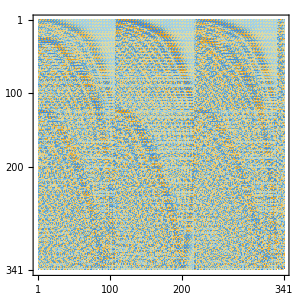

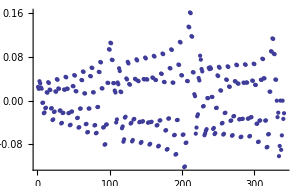

-0.0160281

-3.39745

{-72.2181,-66.8629,-62.1743,-61.9304,-61.0162,-60.796,-59.8912,-59.6823,-58.7823,-58.5808,-57.6836,-57.4878,-56.5921,-56.4014,-55.5061,-55.3205,-54.4245,-54.2442,-53.3464,-53.1721,-52.2711,-52.1037,-51.1979,-51.0385,-50.1264,-49.9762,-49.0562,-48.9161,-47.9868,-47.8576,-46.918,-46.8002,-45.8496,-45.7431,-44.7822,-44.6857,-43.7193,-43.6279,-42.7485,-42.5742,-42.468,-41.5433,-41.5007,-40.4774,-40.4383,-39.4051,-39.3725,-38.3302,-38.3041,-37.2535,-37.2332,-36.1751,-36.1599,-35.0955,-35.0842,-34.0149,-34.0059,-32.9342,-32.9248,-31.8536,-31.8414,-30.7739,-30.7565,-29.7012,-29.6709,-28.7635,-28.5863,-28.4451,-27.5145,-27.4773,-26.9365,-26.4001,-26.369,-25.5526,-25.5234,-25.3135,-25.2867,-24.3821,-24.3593,-24.2238,-24.2002,-23.2398,-23.2249,-23.1301,-23.1082,-22.1152,-22.107,-22.0299,-22.0086,-21.0046,-21.0014,-20.9218,-20.901,-19.904,-19.9026,-19.8082,-19.7879,-18.8094,-18.8054,-18.6929,-18.6723,-17.7163,-17.7094,-17.5775,-17.5556,-16.6232,-16.6135,-16.4626,-16.4385,-15.5298,-15.5173,-15.3482,-15.321,-14.4357,-14.4205,-14.2342,-14.203,-13.341,-13.3228,-13.1205,-13.0844,-12.2455,-12.2241,-12.0067,-11.9648,-11.1494,-11.1244,-10.8928,-10.8439,-10.0533,-10.0236,-9.77823,-9.72126,-8.958,-8.92151,-8.66275,-8.59616,-7.86658,-7.81817,-7.54566,-7.4678,-6.78973,-6.7136,-6.42593,-6.33655,-5.79359,-5.60798,-5.30168,-5.25631,-5.07862,-4.50187,-4.3888,-4.16823,-3.9819,-3.39745,-3.33767,-2.32451,-2.28271,-1.24121,-1.20881,-0.152056,-0.12512,0.94199,0.965646,2.04036,2.06207,3.14252,3.16317,4.24793,4.26811,5.35603,5.37615,6.46626,6.48662,7.40325,7.57815,7.59892,8.69106,8.71212,9.38115,9.79969,9.82872,9.86972,10.4722,10.9152,10.9447,11.0655,11.5098,12.0303,12.0585,12.236,12.5344,13.146,13.1704,13.3946,13.5811,14.2623,14.2818,14.5462,14.6583,15.3792,15.394,15.6931,15.7576,16.4968,16.5073,16.8365,16.8697,17.6149,17.6218,17.977,17.9887,18.7335,18.7374,19.1108,19.1154,19.852,19.8548,20.2346,20.2511,20.9697,20.9743,21.3583,21.3848,22.0875,22.0952,22.4813,22.5164,23.2055,23.2171,23.603,23.6458,24.3237,24.3401,24.7231,24.773,25.4418,25.4642,25.8414,25.8981,26.5592,26.5897,26.9582,27.0208,27.6753,27.7168,28.0737,28.1411,28.7888,28.8457,29.1889,29.2589,29.8981,29.9769,30.3055,30.3739,31.0009,31.1108,31.4263,31.4859,32.0949,32.2483,32.5557,32.5942,33.1784,33.391,33.6952,33.7037,34.2512,34.5422,34.7913,34.8831,35.3156,35.7133,36.3702,36.7745,37.396,37.8525,38.3745,38.9405,39.3197,40.0357,40.2888,41.1363,41.3108,42.2406,42.3731,43.3473,43.4588,44.4553,44.558,45.5635,45.665,46.6706,46.7771,47.7751,47.8926,48.8745,49.0103,49.9641,50.1297,51.0352,51.2503,52.0705,52.3718,53.0481,53.4936,53.9823,54.6157,54.9448,55.7374,55.9689,56.8581,57.0365,57.977,58.128,59.0922,59.2329,60.2003,60.3461,61.2942,61.4648,62.3583,62.5877,63.3624,63.7139,64.2934,64.8432,65.2335,65.9754,66.2538,67.1106,67.3352,68.2491,68.4506,69.3915,69.588,70.539,70.7458,71.6937,71.9352}

0.

```mathematica
(*Admixture of 60s1/2 at 500V/m*)
EField={0,0,500};MatrixPlot[Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]]
ListPlot[Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[116]]]
Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[152,152]]
EField={0,0,500};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[152]]-Subscript[E, 12]/10^9
EField={0,0,500};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9
EField={0,0,0};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[116]]-Subscript[E, 12]/10^9
```

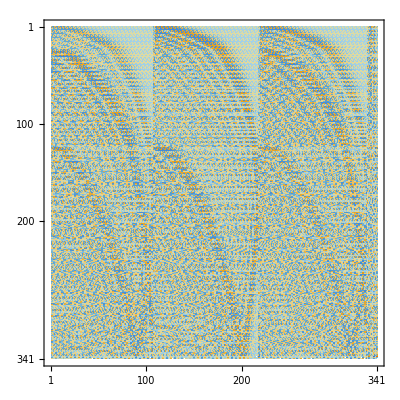

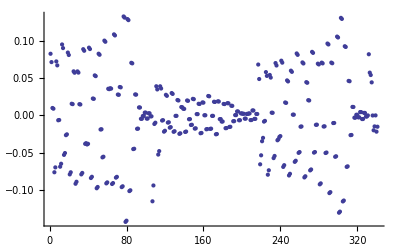

0.0478166

-13.5686

-7.79615

```mathematica
(*Admixture of 58d3/2 at 300V/m*)
EField={0,0,300};MatrixPlot[Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]]
ListPlot[Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[114]]]
Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[114,114]]
EField={0,0,300};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[114]]-Subscript[E, 12]/10^9
EField={0,0,0};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[114]]-Subscript[E, 12]/10^9
```

```mathematica
(*Export data for Origin*)
Clear[i,k,L,MPList,R]
MPList=Array[L,{Length[NList],2}];
Temp={};
EMIN=0;
EMAX=500;


E0=EMIN;
EStep=0.1;

TempList=Array[T,Length[NList]];
For[i=1,i≤Length[NList],i++,TempList[[i]]={i,LabelList[[i]]} ]

Clear[i,k,L,MPList,R]
E0=EMIN;;
MPList={};
MPList=Join[MPList,{Join[{E0},Array[#&,Length[NList]]] }];
MPList=Join[MPList,{Join[{E0},LabelList] }];
While[E0<EMAX,E0=E0+EStep;EField={0,0,E0};Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9;MPList=Join[MPList,{Join[{E0},Temp] }] ] 
Export[FileNameJoin[{Directory[],"Starkshift3.dat"}],MPList]
Export[FileNameJoin[{Directory[],"Starkbase3.dat"}],TempList]
```

C:\Documents and Settings\R14\Mes documents\Starkshift3.dat

C:\Documents and Settings\R14\Mes documents\Starkbase3.dat

```mathematica
⁃Graphics⁃⁃Graphics⁃ n=15 -18, ninitial=15, Subscript[m, j]=1/2
```

⁃Graphics⁃

⁃Graphics⁃

⁃Graphics⁃

```mathematica
⁃Graphics⁃ n=15-17 , Subscript[m, j]=5/2, n initial=15.
```

⁃Graphics⁃

⁃Graphics⁃

```mathematica
⁃Graphics⁃Shift of 44s44s [GHz]  at R=∞, E  in  V/m, 212  level, n=42 to 46, all M, l=s,p, EField =(0,0,E0)
```

```mathematica
⁃Graphics⁃Shift of 44s44s [GHz]  at R=∞, E  in  V/m, 212  level, n=42 to 46, all M, l=s,p
```

```mathematica
⁃Graphics⁃ Stark-Shift of 44s44s [GHz]  at R=∞, E  in  V/m, 350 level, n=41 to 47, M=1
```

```mathematica
⁃Graphics⁃ Stark-Shift of 44s44s [GHz]  at R=∞, E in V/m, 147 level, n=42 to 46, M=1
```